```mathematica
(* -- Torpedo Inertial Transforms calculation --*)
```

```mathematica
(* -- Determining rotation and new inertial axii --*)
```

```mathematica
(*Known moments of inertia around the primary axii of bar*)
```

```mathematica
MoIBAR = {Ixx -> 0.01, Ixy -> 0, Ixz -> 0,Iyx -> 0, Iyy -> 0.6, Iyz -> 0,Izx -> 0, Izy -> 0, Izz -> 0.6}
```

{Ixx→0.01,Ixy→0,Ixz→0,Iyx→0,Iyy→0.6,Iyz→0,Izx→0,Izy→0,Izz→0.6}

```mathematica
(* Making a Dummy Moment of Inertia Matrix to hold the size of the tensor to be used. *)
```

```mathematica
MoI = {{Ixx, Ixy, Ixz},{Iyx, Iyy, Iyz},{Izx, Izy, Izz}}
```

{{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}}

```mathematica
(*Location of the suspension point compared to CoM in bar reference frame*)
```

```mathematica
A[deltax_, deltay_, deltaz_] := {deltax, deltay, deltaz};
```

```mathematica
(*Rotational Functions*)
```

```mathematica
Yaw[alpha_] := {{Cos[alpha], -Sin[alpha], 0} ,{Sin[alpha], Cos[alpha], 0},{ 0,0,1}};
```

```mathematica
Pitch[beta_] := {{Cos[beta], 0, Sin[beta]} ,{0, 1, 0},{ -Sin[beta],0,Cos[beta]}};
```

```mathematica
Roll[gamma_] := {{ 1,0,0},{0,Cos[gamma], -Sin[gamma]} ,{0,Sin[gamma], Cos[gamma]}};
```

```mathematica
Rotation[alpha_, beta_,gamma_]:=Yaw[alpha].Pitch[beta].Roll[gamma];
```

```mathematica
ReverseRotation[alpha_, beta_,gamma_]:=Roll[-gamma].Pitch[-beta].Yaw[-alpha];
```

```mathematica
(*Determining the new moments of inertia in lab reference frame*)
```

```mathematica
MoICOM[alpha_, beta_,gamma_] :=ReverseRotation[alpha, beta,gamma].MoI.Transpose[ReverseRotation[alpha, beta,gamma]];
```

```mathematica
(*Determining the displacement vector of the suspension point from CoM with this rotation in lab reference frame*)
```

```mathematica
B[deltax_, deltay_, deltaz_, alpha_, beta_,gamma_]:= A[deltax, deltay, deltaz].Rotation[alpha, beta,gamma];
```

```mathematica
(*  -- Making the Lagrangian --  *)
```

```mathematica
(* Location of the CoM taking the coordinate system at the pivot point *)
```

```mathematica
S[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_] := {x0,y0,z0} - B[deltax, deltay, deltaz, alpha, beta,gamma]
```

```mathematica
(* Moments of Inertia around this point using parrallel axis theorem *)
```

```mathematica
Ir[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_, mass_] := MoICOM[alpha, beta,gamma]+mass*((S[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma]^2).IdentityMatrix[3] - Outer[Times,S[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma], S[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma]]);
```

```mathematica
(* - Determining the kinetic energy of the system - *)
```

```mathematica
LinearEnergy[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_, mass_] := (1/2)*mass*(D[S[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma],t].D[S[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma],t])
```

```mathematica
RotationalEnergy[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_, mass_] := (1/2)*Total[MoICOM[alpha, beta,gamma].({{(D[alpha,t]^2),0,0},{0,0,0},{0,0,0}}+{{0,0,0},{0,D[beta,t]^2,0},{0,0,0}}+{{0,0,0},{0,0,0},{0,D[gamma,t]^2,0}}),2]
```

```mathematica
TotalKinetic[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_, mass_] := LinearEnergy[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma, mass] +RotationalEnergy[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma, mass];
```

```mathematica
(* - Determining the potential energy of the system - *)
```

```mathematica
RotatorySpringPotential[alpha_, beta_,gamma_ ,Ka_,Kb_,Kg_]:= (1/2)*((Ka*alpha^2)+(Kb*beta^2)+(Kg*gamma^2));
```

```mathematica
GravitationalPotential[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_, mass_,gravity_]:= -{0,0,gravity*mass}.S[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma];
```

```mathematica
TotalPotential[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_,Ka_,Kb_,Kg_, mass_,gravity_] := RotatorySpringPotential[alpha, beta,gamma ,Ka,Kb,Kg]+GravitationalPotential[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma, mass,gravity];
```

```mathematica
(* - Forming the Lagrangian - *)
```

```mathematica
BarLagrangian[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_,Ka_,Kb_,Kg_, mass_,gravity_] := TotalKinetic[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma, mass] - TotalPotential[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity]
```

```mathematica
(* -- Forming the equations of motion -- *)
```

```mathematica
(* - motion in alpha(YAW) - *)
```

```mathematica
AlphaRHS[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_,Ka_,Kb_,Kg_, mass_,gravity_] := D[(D[BarLagrangian[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity], D[alpha,t]] ),t]- D[BarLagrangian[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity], alpha]
```

```mathematica
(* - motion in beta(PITCH) - *)
```

```mathematica
BetaRHS[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_,Ka_,Kb_,Kg_, mass_,gravity_] := D[(D[BarLagrangian[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity], D[beta,t]] ),t]- D[BarLagrangian[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity], beta]
```

```mathematica
(* - motion in gamma(ROLL) - *)
```

```mathematica
GammaRHS[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_,Ka_,Kb_,Kg_, mass_,gravity_] := D[(D[BarLagrangian[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity], D[gamma,t]] ),t]- D[BarLagrangian[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity], gamma]
```

```mathematica
(* - Forming the series of equations - *)
```

```mathematica
MotionEqs[x0_,y0_,z0_,deltax_, deltay_, deltaz_, alpha_, beta_,gamma_,Ka_,Kb_,Kg_, mass_,gravity_] := {0 == AlphaRHS[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity] ,
0 == BetaRHS[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity] ,
0 == GammaRHS[x0,y0,z0,deltax, deltay, deltaz, alpha, beta,gamma,Ka,Kb,Kg, mass,gravity] }
```

```mathematica
(* Testing *)
```

```mathematica
Ir[0,0,0,2, 0, 0, 0, 0,0, 1]
```

{{Ixx,4+Ixy,4+Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}}

```mathematica
(* Specifying the System of equations with dependant and independant variables *)
```

```mathematica
SystemEqs = MotionEqs[x0[t],y0[t],z0[t],Δx, Δy, Δz, α[t], β[t],γ[t],Ka,Kb,Kg, m,g];
```

```mathematica
(* Applying a first-order small angle approximation *)
```

```mathematica
SmallSystemEqs = SystemEqs /.{Sin[α[t]]->α[t],Sin[β[t]]->β[t],Sin[γ[t]]->γ[t],Cos[α[t]]->1-(α[t]^2)/2,Cos[β[t]]->1-(β[t]^2)/2,Cos[γ[t]]->1-(γ[t]^2)/2};
```

```mathematica
(* Deleting and third order or higher angular terms *)
```

```mathematica
HSRSystemEqs =Expand[SmallSystemEqs] /.{α[t]^k_/;k>2->0,β[t]^k_/;k>2->0,γ[t]^k_/;k>2->0,α[t]*β[t]^k_/;k>1->0,α[t]^k_*β[t]/;k>1->0,γ[t]*β[t]^k_/;k>1->0,γ[t]^k_*β[t]/;k>1->0, γ[t]*α[t]^k_/;k>1->0,γ[t]^k_*α[t]/;k>1->0,α[t]^2*β[t]^k_/;k>0->0,α[t]^k_*β[t]^2/;k>0->0,γ[t]^2*β[t]^k_/;k>0->0,γ[t]^k_*β[t]^2/;k>0->0, γ[t]^2*α[t]^k_/;k>0->0,γ[t]^k_*α[t]^2/;k>0->0,α[t]*β[t]*γ[t]->0};
```

```mathematica
(* Finding the Laplace Transform *)
```

```mathematica
TransformedEqs =LaplaceTransform[HSRSystemEqs,t,s];
```

```mathematica
LaplaceForm = TransformedEqs /.{LaplaceTransform[y0[t],t,s]->Y[s],LaplaceTransform[x0[t],t,s]->X[s],LaplaceTransform[z0[t],t,s]->Z[s],LaplaceTransform[α[t],t,s]->Ry[s],LaplaceTransform[β[t],t,s]->Rp[s],LaplaceTransform[γ[t],t,s]->Rr[s],y0[0]->0,y0'[0]->0,y0''[0]->0,x0[0]->0,x0'[0]->0,x0''[0]->0,z0[0]->0,z0'[0]->0,z0''[0]->0,α'[0]->0,β'[0]->0,γ'[0]->0};
```

```mathematica
(* Dropping Cross coupling terms *)
```

```mathematica
SimpLaplaceForm = LaplaceForm  /.{γ[t]->0,γ'[t]->0,γ''[t]->0,β[t]->0,β'[t]->0,β''[t]->0,α[t]->0,α'[t]->0,α''[t]->0}
```

{0==g m Δy Rp[s]+g m Δx Rr[s]+Ka Ry[s]-m s^2 Δy X[s]+m s^2 Δx Y[s]+Ixx (s^2 Ry[s]-s α[0])+Iyx (s^2 Ry[s]-s α[0])+Izx (s^2 Ry[s]-s α[0])+m Δx^2 (s^2 Ry[s]-s α[0])+m Δy^2 (s^2 Ry[s]-s α[0])-m Δy Δz (s^2 Rp[s]-s β[0])-m Δx Δz (s^2 Rr[s]-s γ[0]),0==(g m Δx)/s+Kb Rp[s]-g m Δz Rp[s]+g m Δy Ry[s]+m s^2 Δz X[s]-m s^2 Δx Z[s]-m Δy Δz (s^2 Ry[s]-s α[0])+Ixy (s^2 Rp[s]-s β[0])+Iyy (s^2 Rp[s]-s β[0])+Izy (s^2 Rp[s]-s β[0])+m Δx^2 (s^2 Rp[s]-s β[0])+m Δz^2 (s^2 Rp[s]-s β[0])-m Δx Δy (s^2 Rr[s]-s γ[0]),0==-(g m Δy)/s+Kg Rr[s]-g m Δz Rr[s]+g m Δx Ry[s]-m s^2 Δz Y[s]+m s^2 Δy Z[s]-m Δx Δz (s^2 Ry[s]-s α[0])-m Δx Δy (s^2 Rp[s]-s β[0])+Ixz (s^2 Rr[s]-s γ[0])+Iyz (s^2 Rr[s]-s γ[0])+Izz (s^2 Rr[s]-s γ[0])+m Δy^2 (s^2 Rr[s]-s γ[0])+m Δz^2 (s^2 Rr[s]-s γ[0])}

```mathematica
(* Finding a solution *)
```

```mathematica
SolvedEqs = Collect[Solve[SimpLaplaceForm, {Ry[s], Rp[s], Rr[s]}][[1]], {X[s], Y[s], Z[s]}];
```

```mathematica
(* Finding a Transfer Function of Ry[s]/{X[s],Y[s],Z[s]} *)
```

```mathematica
RySingleMode  = Ry[s]/.SolvedEqs;
```

```mathematica
RyXTransfer = (((RySingleMode /.{Y[s]-> 0, Z[s]-> 0})-(RySingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{X[s]-> 1})/.{s -> I*w};
```

```mathematica
RyYTransfer = (((RySingleMode /.{X[s]-> 0, Z[s]-> 0})-(RySingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{Y[s]-> 1})/.{s -> I*w};
```

```mathematica
RyZTransfer = (((RySingleMode /.{X[s]-> 0, Y[s]-> 0})-(RySingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{Z[s]-> 1})/.{s -> I*w};
```

```mathematica
(* Finding a Transfer Function of Rp[s]/{X[s],Y[s],Z[s]} *)
```

```mathematica
RpSingleMode  = Rp[s]/.SolvedEqs;
```

```mathematica
RpXTransfer = (((RpSingleMode /.{Y[s]-> 0, Z[s]-> 0})-(RpSingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{X[s]-> 1})/.{s -> I*w};
```

```mathematica
RpYTransfer = (((RpSingleMode /.{X[s]-> 0, Z[s]-> 0})-(RpSingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{Y[s]-> 1})/.{s -> I*w};
```

```mathematica
RpZTransfer = (((RpSingleMode /.{X[s]-> 0, Y[s]-> 0})-(RpSingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{Z[s]-> 1})/.{s -> I*w};
```

```mathematica
(* Finding a Transfer Function of Rr[s]/{X[s],Y[s],Z[s]} *)
```

```mathematica
RrSingleMode  = Rr[s]/.SolvedEqs;
```

```mathematica
RrXTransfer = (((RrSingleMode /.{Y[s]-> 0, Z[s]-> 0})-(RrSingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{X[s]-> 1})/.{s -> I*w};
```

```mathematica
RrYTransfer = (((RrSingleMode /.{X[s]-> 0, Z[s]-> 0})-(RrSingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{Y[s]-> 1})/.{s -> I*w};
```

```mathematica
RrZTransfer = (((RrSingleMode /.{X[s]-> 0, Y[s]-> 0})-(RrSingleMode /.{X[s]-> 0, Z[s]-> 0, Y[s]-> 0}))/.{Z[s]-> 1})/.{s -> I*w};
```

```mathematica
(* Making a transfer function matrix *)
```

```mathematica
RTransferMat = {{RrXTransfer, RpXTransfer,RyXTransfer}, {RrYTransfer, RpYTransfer,RyYTransfer},{RrZTransfer, RpZTransfer,RyZTransfer}};
```

```mathematica
(* Writing to Matlab *)
```

```mathematica
RTransMat = RTransferMat /.{Δx->deltax, Δy->deltay,Δz->deltaz, α[0]->alpha0,γ[0] ->gamma0,β[0] ->beta0,Ka->Ky,Kb->Kp, Kg->Kr} ;
```

```mathematica
ToMatlab[RTransMat];
```

```mathematica
(* Directory[]
```

```mathematica
(* C:\\Users\\Shadow\\Documents"
```

```mathematica
(* file = OpenWrite["RTransMatrix.m"]
```

```mathematica
(*WriteMatlab[RTransMat , file, "RTransMat"]*)
```

```mathematica
(* Close[file]
```

```mathematica
(* Trying real approximate numbers *)
```

```mathematica
TestSim = Simplify[RyYTransfer /.{Δx->100*(10^-6), Δy->85*(10^-3),Δz->100*(10^-6), α[0]->0,γ[0] ->0, β[0] ->0, Ixx->0.1,Iyy->0.6,Izz->0.6, g->9.8, m->13.6,Ka->0.0002,Kb->0.0002, Kg->0.0258, s-> I*w}/. MoIBAR]
```

(-5.32494×10^-11 w^4-1.19844×10^-9 w^6+6.58666×10^-8 w^8)/(3.38813×10^-21-0.000185038 w^2+0.0103596 w^4+1.82522×10^-7 w^6-9.602×10^-6 w^8)

```mathematica
(* Trying to Display a Spectra *)
```

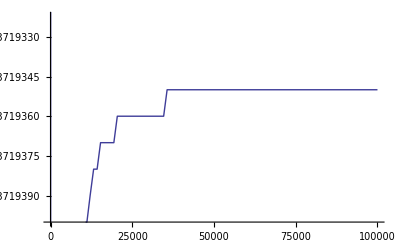

```mathematica
Plot[Re[TestSim],{w,0, 100000}]
```